```mathematica
Clear[p];
p=Table[0,{i,0,Pi/2,0.01}];
j=1;
Table[{
(*参数设置*)
g=10;
l=1;
m=1;
θi=h;(*初始角度*)
xc=l/2 Sin[θ[t]];
xcp=D[xc,t];
L=1/2 m*xcp^2+1/2*1/12 m*l^2(xcp/(l/2 Cos[θ[t]]))^2-m*g*xc;
(*生成演化方程*)
eq1=D[L,θ[t]]==D[D[L,θ'[t]],t];
θv=0;
(*初始角速度*)
sol=NDSolve[{
eq1,
θ[0]==θi,
θ'[0]==θv
},{θ},{t,0,1}];
(*赋值*)
θr=θ/.sol[[1]];
(*画图*)
data=Table[{t,θr[t]},{t,0,1,0.001}];
Do[{If[data[[i,2]]<0,{p[[j]]={h,data[[i,1]]},j++,Break[];},];},{i,1,Length[data]}];
},{h,0,Pi/2,0.01}];
```

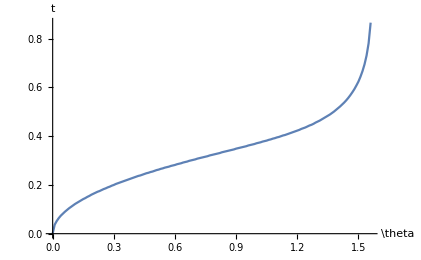

```mathematica
ListLinePlot[p,AxesLabel->{RawBoxes[RowBox[{"\\","theta"}]],HoldForm[t]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```